## LOAD OPTEX

```mathematica
SetDirectory[NotebookDirectory[]];
<<OptEx.m
<<CustomPlotFunctions.m
```

OptEx-1.0

Sunando K. Patra
 Bangabasi Evening College, Univ. of Calcutta
 West Bengal, India

If you are using OptEx for the first time, try running ' OptExHelp[ ]; '.

### Replace Lists

These lists define the relations amongst the SM couplings, masses etc.

```mathematica
lstcoupling={gS->√(4 π alphas),gW->(2 √(π alpha))/s,gY->(2 √(π alpha))/c,SMYd->(√2 mb)/v,SMYe->(√2 mtau)/v,SMYu->(√2 mt)/v,l-> 1/(√(√2 gf)),λhSM-> mh^2/(2 v^2)};
lstexp={v->1/(√(√2 gf)),s->√(1/2-1/2 √(1-(4 π alpha)/(√2 gf mz^2))),c->√(1/2+1/2 √(1-(4 π alpha)/(√2 gf mz^2)))};
lstval={gf->0.000011663787000000001,alpha->7.2973525664*10^-3,mb-> 4.18,mtau-> 1.77};
rplst=lstcoupling/.lstexp/.lstval;
replstwc=<|"q1Hl[1,1]"->"q1Hl11","q1Hq[1,1]"->"q1Hq11","q3Hl[1,1]"->"q3Hl11","q3Hq[1,1]"->"q3Hq11","qdH[1,1]"->"qdH11","qeH[1,1]"->"qeH11","qH"->"qH","qHB"->"qHB","qHbox"->"qHbox","qHD"->"qHD","qHd[1,1]"->"qHd11","qHe[1,1]"->"qHe11","qHG"->"qHG","qHu[1,1]"->"qHu11","qHW"->"qHW","qHWB"->"qHWB","qll[1,1,1,1]"->"qll1111","quH[1,1]"->"quH11"|>;
```

```mathematica
stringlstnp=<|q1Hl11->"\!\(\*SubsuperscriptBox[\"𝒞\", \"Hl\", \"(1)\"]\)",q1Hq11->"\!\(\*SubsuperscriptBox[\"𝒞\", \"Hq\", \"(1)\"]\)",q3Hl11->"\!\(\*SubsuperscriptBox[\"𝒞\", \"Hl\", \"(3)\"]\)",q3Hq11->"\!\(\*SubsuperscriptBox[\"𝒞\", \"Hq\", \"(3)\"]\)",qdH11->"\!\(\*SubscriptBox[\"𝒞\", \"dH\"]\)",qeH11->"\!\(\*SubscriptBox[\"𝒞\", \"eH\"]\)",qH->"\!\(\*SubscriptBox[\"𝒞\", \"H\"]\)",qHB->"\!\(\*SubscriptBox[\"𝒞\", \"HB\"]\)",qHbox->"\!\(\*SubscriptBox[\"𝒞\", RowBox[{\"H\", \" \", \"□\"}]]\)",qHD->"\!\(\*SubscriptBox[\"𝒞\", \"HD\"]\)",qHd11->"\!\(\*SubscriptBox[\"𝒞\", \"Hd\"]\)",qHe11->"\!\(\*SubscriptBox[\"𝒞\", \"He\"]\)",qHG->"\!\(\*SubscriptBox[\"𝒞\", \"HG\"]\)",qHu11->"\!\(\*SubscriptBox[\"𝒞\", \"Hu\"]\)",qHW->"\!\(\*SubscriptBox[\"𝒞\", \"HW\"]\)",qHWB->"\!\(\*SubscriptBox[\"𝒞\", \"HWB\"]\)",qll1111->"\!\(\*SubscriptBox[\"𝒞\", \"ll\"]\)",quH11->"\!\(\*SubscriptBox[\"𝒞\", \"uH\"]\)",mz->"\!\(\*SubscriptBox[\(m\), \(z\)]\)",alphas->"\!\(\*SubscriptBox[\(α\), \(s\)]\)",mh->"\!\(\*SubscriptBox[\(m\), \(H\)]\)",halpha->"\!\(\*SubsuperscriptBox[\(Δα\), \(had\), \((5)\)]\)(\!\(\*SubsuperscriptBox[\(m\), \(Z\), \(2\)]\))",mt->"\!\(\*SubscriptBox[\(m\), \(t\)]\)"|>
```

<|q1Hl11→𝒞_Hl^(1),q1Hq11→𝒞_Hq^(1),q3Hl11→𝒞_Hl^(3),q3Hq11→𝒞_Hq^(3),qdH11→𝒞_dH,qeH11→𝒞_eH,qH→𝒞_H,qHB→𝒞_HB,qHbox→𝒞_(H □),qHD→𝒞_HD,qHd11→𝒞_Hd,qHe11→𝒞_He,qHG→𝒞_HG,qHu11→𝒞_Hu,qHW→𝒞_HW,qHWB→𝒞_HWB,qll1111→𝒞_ll,quH11→𝒞_uH,mz→m_z,alphas→α_s,mh→m_H,halpha→Δα_had^(5)(m_Z^2),mt→m_t|>

## SM Fit

Load SM fit result :

```mathematica
smrun=loadRun["ewpoSM_run"];
```

```mathematica
smrun["Parameters"]
```

{mz,alphas,mh,halpha,mt}

One- and two-dimensional posterior distributions among the SM parameters along with their fit results :

```mathematica
stringlstSM=AssociationThread[{mz,alphas,mh,halpha,mt},{"m_z","α_s","m_H","Δα_had^(5)(m_Z^2)","m_t"}]
```

<|mz→m_z,alphas→α_s,mh→m_H,halpha→Δα_had^(5)(m_Z^2),mt→m_t|>

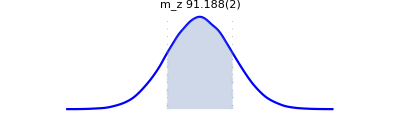
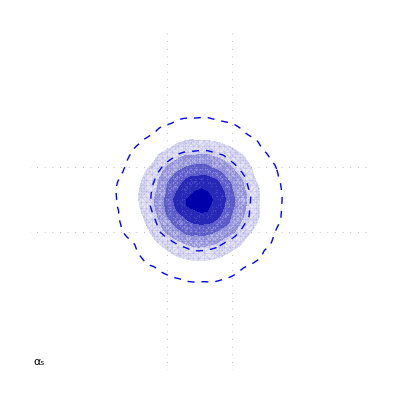
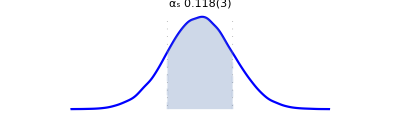
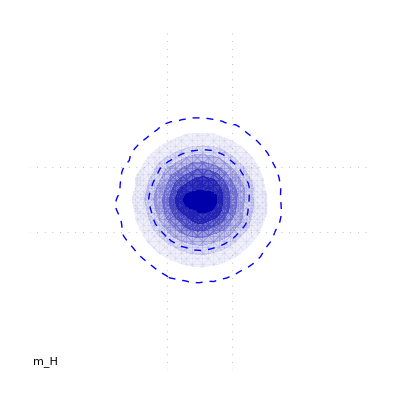
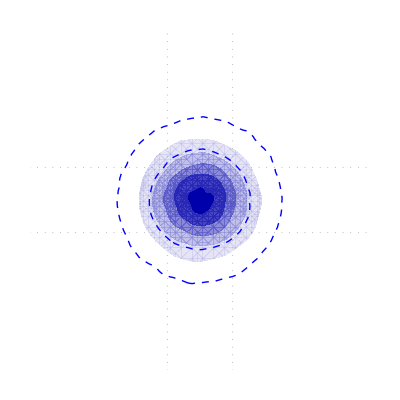
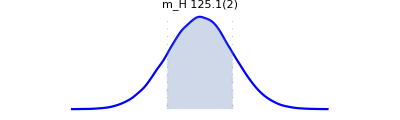
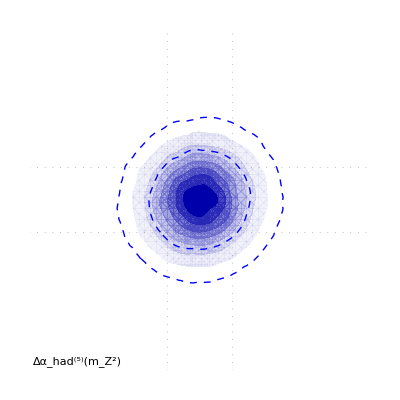
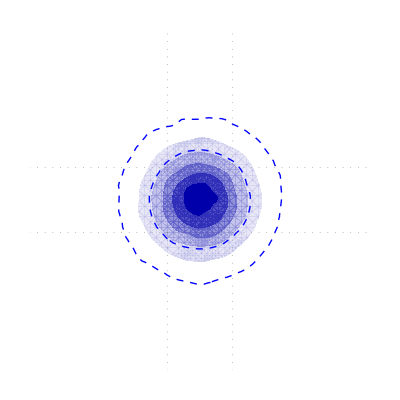
-Graphics- |  |  |  | 
-Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Framed[Grid[Table[triPlotBayesPart[smrun,5,i,j,stringlstSM],{i,Length@stringlstSM},{j,Length@stringlstSM}]]]
```

Correlation matrix obtained for the SM fit result

```mathematica
smrun["CorrelationMatrix"]
```

(1. | -0.00706315 | 0.00240272 | 0.0400104 | -0.0973544
-0.00706315 | 1. | -0.000869088 | 0.0101092 | 0.0451365
0.00240272 | -0.000869088 | 1. | -0.00139714 | 0.00204836
0.0400104 | 0.0101092 | -0.00139714 | 1. | 0.0985241
-0.0973544 | 0.0451365 | 0.00204836 | 0.0985241 | 1.)

SM fit parameters are used as nuisance parameters in the SMEFT fits and the fit results are considered a multi-normal priors.

## Model Independent Fits

Load fit results of the 18 WCs contributing to EWPO and Higgs signal strength data   :

```mathematica
np18wcrun=loadRun["np18wc"]
```

MCMCResult[{q1Hl11→0.0477885,q1Hq11→-0.016264,q3Hl11→0.574295,q3Hq11→0.518185,qdH11→0.086892,qeH11→0.00372067,qH→-0.190312,qHB→-0.000352853,qHbox→-1.00625,qHD→0.398668,qHd11→-0.586262,qHe11→0.0591221,qHG→-0.00182364,qHu11→0.0868878,qHWB→-0.244073,qll1111→0.233392,quH11→0.0280639,qHW→-7.81842,mz→91.1881,alphas→0.118313,mh→125.098,halpha→0.0275686,mt→173.437},«200000»]

1D and 2D marginal posteriors for the 18 WCs showing their fit results and the correlations

```mathematica
stringlstnp1=Module[{wc,lst1,lst2,lst3,lst4,lstwc},
wc=ToString[#]&/@Drop[np18wcrun["Parameters"],-5];
lst1=StringDrop[#,1]&/@wc;
lst2=DeleteCases[If[(StringMatchQ[#,__~~"11"]==True),#]&/@lst1,Null];
lst3=Complement[lst1,lst2];
lst4=StringDrop[lst2,-2];
lstwc=(Subscript[𝒞,ToExpression[#]]&/@Union[lst3,lst4])/.{Subscript[𝒞, ll11]-> Subscript[𝒞, ll],Subscript[𝒞, Hbox]-> 𝒞_(H□),Subscript[𝒞, 3 Hq]-> Subscript[𝒞, Hq]^(3),Subscript[𝒞, 3 Hl]-> Subscript[𝒞, Hl]^(3),Subscript[𝒞, 1 Hl]-> Subscript[𝒞, Hl]^(1),Subscript[𝒞, 1 Hq]-> Subscript[𝒞, Hq]^(1)};
AssociationThread[Join[ToExpression/@Union[wc],{mz,alphas,mh,halpha,mt}],Join[ToString[#,FormatType-> StandardForm]&/@lstwc,{"m_z","α_s","m_H","Δα_had^(5)(m_Z^2)","m_t"}]]];
```

```mathematica
Grid[Table[triPlotBayesPart[np18wcrun,5,i,j,stringlstnp ],{i,18},{j,18}]];
```

Load fit results of the 10 WCs     :

```mathematica
np10wcrun=loadRun["np10wc"]
```

1D and 2D marginal posteriors for the 10 WCs showing their fit results and the correlations:

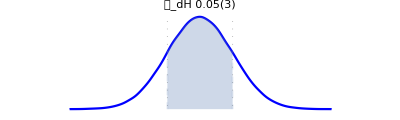
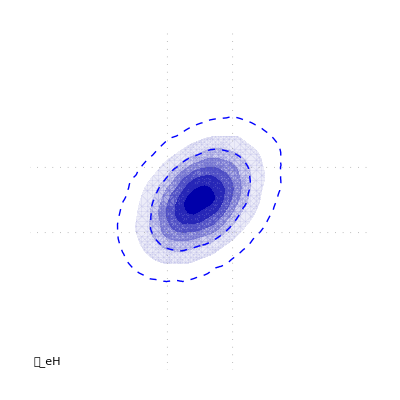
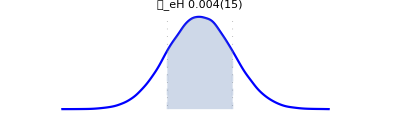
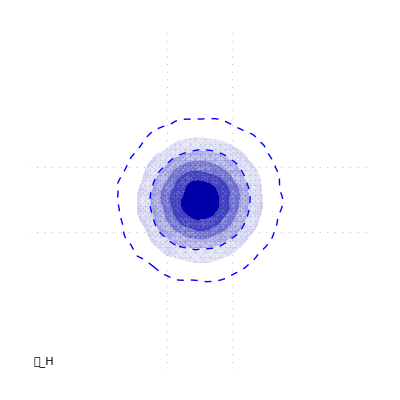
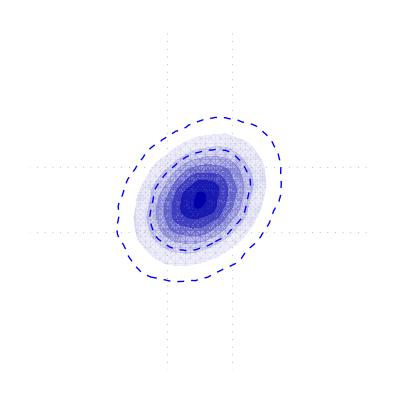
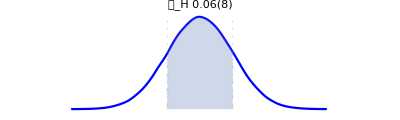
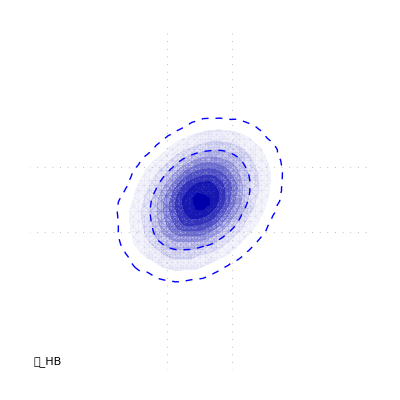
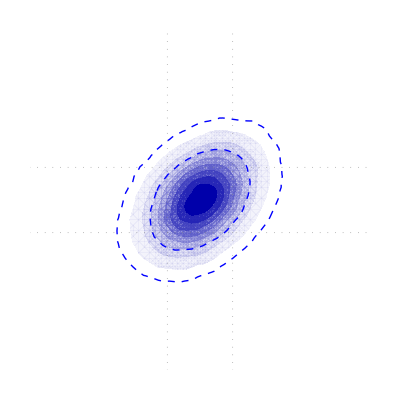
-Graphics- |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[Table[triPlotBayesPart[np10wcrun,5,i,j,stringlstnp ],{i,10},{j,10}]]
```

## Model Dependent Fits

### BSM class of color-singlet Isospin-multiplet complex scalars comprising SM+ℋ_2, SM+ Δ_1 and SM+Σ

#### Load the matching results:

```mathematica
matchwcH2=Import[FileNameJoin[{NotebookDirectory[],"wcs","H2_match.m"}]];
```

```mathematica
matchwcDelta1=Import[FileNameJoin[{NotebookDirectory[],"wcs","Delta1_match.m"}]];
```

```mathematica
matchwcSigma=Import[FileNameJoin[{NotebookDirectory[],"wcs","Sigma_match.m"}]];
```

#### Load Wilson coefficient fit result (model parameter independent):

```mathematica
fitwcH2=loadRun["H2wc"];
```

```mathematica
stringlstwc=Module[{wc,wc1,lst1,lst2},
wc=matchwcH2[[2]][[All,1]];
wc1=StringDelete[StringReplace[#,((#-> "m")&/@{"[",",","]"})],"m"]&/@wc;
lst1=StringDelete[StringDrop[#,1],DigitCharacter]&/@wc1;
lst2=(Subscript[𝒞,ToExpression[#]]&/@lst1)/.{Subscript[𝒞, ll1111]-> Subscript[𝒞, ll]};
AssociationThread[Join[ToExpression/@wc1,{mz,alphas,mh,halpha,mt}],Join[(ToString[#,FormatType-> StandardForm]&/@lst2)/.{"\!\(\*SubscriptBox[\"𝒞\", \"Hbox\"]\)"-> "𝒞_(H □)"},{"m_z","α_s","m_H","Δα_had^(5)(m_Z^2)","m_t"}]]]
```

<|q1lequ1111→𝒞_lequ,q1qd1111→𝒞_qd,q1qu1111→𝒞_qu,q1quqd1111→𝒞_quqd,qdH11→𝒞_dH,qeH11→𝒞_eH,qH→𝒞_H,qHB→𝒞_HB,qHbox→𝒞_(H □),qHD→𝒞_HD,qHW→𝒞_HW,qHWB→𝒞_HWB,qle1111→𝒞_le,qledq1111→𝒞_ledq,quH11→𝒞_uH,qW→𝒞_W,mz→m_z,alphas→α_s,mh→m_H,halpha→Δα_had^(5)(m_Z^2),mt→m_t|>

#### Load model parameter fit result (model parameter dependent):

```mathematica
fitwcparamH2=loadRun["H2param"];
```

```mathematica
fitwcparamDelta1=loadRun["Delta1param"];
```

```mathematica
fitwcparamSigma=loadRun["Sigmaparam"];
```

```mathematica
stringlstH2=AssociationThread[fitwcparamH2["Parameters"],{"λ_ℋ_2","λ_ℋ_2","λ_ℋ_2","m_z","α_s","m_H","Δα_had^(5)","m_t"}]
```

<|λℋ21→λ_ℋ_2,λℋ22→λ_ℋ_2,λℋ23→λ_ℋ_2,mz→m_z,alphas→α_s,mh→m_H,halpha→Δα_had^(5),mt→m_t|>

```mathematica
stringlstDelta1=AssociationThread[fitwcparamDelta1["Parameters"],{"λ_Δ_1","λ_Δ_1","μ_Δ_1","m_z","α_s","m_H","Δα_had^(5)","m_t"}]
```

<|λΔ11→λ_Δ_1,λΔ14→λ_Δ_1,μΔ1→μ_Δ_1,mz→m_z,alphas→α_s,mh→m_H,halpha→Δα_had^(5),mt→m_t|>

```mathematica
stringlstSigma=AssociationThread[fitwcparamSigma["Parameters"],{"ζ_1","ζ_2","μ_Σ","m_z","α_s","m_H","Δα_had^(5)","m_t"}]
```

<|ζ1→ζ_1,ζ2→ζ_2,μΣ→μ_Σ,mz→m_z,alphas→α_s,mh→m_H,halpha→Δα_had^(5),mt→m_t|>

1D and 2D marginal posteriors for the SM+ℋ_2 showing their fit results and  correlations.

```mathematica
Framed[Grid[Table[triPlotBayesPart[fitwcparamH2,5,i,j,stringlstH2],{i,3},{j,3}]]]
```

-Graphics- |  | 
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

#### We show 2D posterior derived from Wilson coefficients (parameter independent) fit:

#### qHBqHW

```mathematica
colorlst=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
Flatten[Position[fitwcH2["Parameters"],#]&/@{qHB,qHW}]
```

{4,9}

```mathematica
rangeMod49={{-0.0004,0.0004},{-0.0016,0.0018}};
```

```mathematica
matchwcH2
```

{{gW,gY,mℋ2,SMYd,SMYe,SMYu,yd,ye,yu,λhSM,λℋ2,λℋ21,λℋ22,λℋ23},{{q1lequ[1,1,1,1],(ye yu)/(2 mℋ2^2)+(3 ye yu λℋ2)/(64 mℋ2^2 π^2)},{q1qd[1,1,1,1],-yd^2/(4 mℋ2^2)-(3 yd^2 λℋ2)/(128 mℋ2^2 π^2)},{q1qu[1,1,1,1],-yu^2/(4 mℋ2^2)-(3 yu^2 λℋ2)/(128 mℋ2^2 π^2)},{q1quqd[1,1,1,1],-(yd yu)/(2 mℋ2^2)-(3 yd yu λℋ2)/(64 mℋ2^2 π^2)},{qdH[1,1],(SMYd λℋ22^2)/(192 mℋ2^2 π^2)+(SMYd λℋ23^2)/(48 mℋ2^2 π^2)},{qeH[1,1],(SMYe λℋ22^2)/(192 mℋ2^2 π^2)+(SMYe λℋ23^2)/(48 mℋ2^2 π^2)},{qH,-λℋ21^3/(48 mℋ2^2 π^2)-(λℋ21^2 λℋ22)/(32 mℋ2^2 π^2)+(λhSM λℋ22^2)/(48 mℋ2^2 π^2)-(λℋ21 λℋ22^2)/(32 mℋ2^2 π^2)-λℋ22^3/(96 mℋ2^2 π^2)+(λhSM λℋ23^2)/(12 mℋ2^2 π^2)-(λℋ21 λℋ23^2)/(8 mℋ2^2 π^2)-(λℋ22 λℋ23^2)/(8 mℋ2^2 π^2)},{qHB,(gY^2 λℋ21)/(384 mℋ2^2 π^2)+(gY^2 λℋ22)/(768 mℋ2^2 π^2)},{qHbox,-λℋ21^2/(96 mℋ2^2 π^2)-(λℋ21 λℋ22)/(96 mℋ2^2 π^2)+λℋ22^2/(384 mℋ2^2 π^2)+λℋ23^2/(96 mℋ2^2 π^2)},{qHD,-λℋ22^2/(96 mℋ2^2 π^2)+λℋ23^2/(24 mℋ2^2 π^2)},{qHW,(gW^2 λℋ21)/(384 mℋ2^2 π^2)+(gW^2 λℋ22)/(768 mℋ2^2 π^2)},{qHWB,(gW gY λℋ22)/(192 mℋ2^2 π^2)},{qle[1,1,1,1],-ye^2/(4 mℋ2^2)-(3 ye^2 λℋ2)/(128 mℋ2^2 π^2)},{qledq[1,1,1,1],(yd ye)/(2 mℋ2^2)+(3 yd ye λℋ2)/(64 mℋ2^2 π^2)},{quH[1,1],(SMYu λℋ22^2)/(192 mℋ2^2 π^2)+(SMYu λℋ23^2)/(48 mℋ2^2 π^2)},{qW,gW^3/(5760 mℋ2^2 π^2)}}}

```mathematica
wcparam2hdm49=wcPlotFromModel[fitwcparamH2,matchwcH2,{λℋ2-> 0,mℋ2-> 1000,Λ-> 1000},{qHB,qHW},Red,{1,2},rangeMod49*1.1];
```

```mathematica
wcparamquart49=wcPlotFromModel[fitwcparamSigma,matchwcSigma,{λ2-> 0,mΣ-> 1000,Λ-> 1000},{qHB,qHW},Blue,{1,2},rangeMod49*1.1];
```

```mathematica
wcparamct49=wcPlotFromModel[fitwcparamDelta1,matchwcDelta1,{mΔ1->1000,Λ-> 1000,λΔ12-> 0,λΔ13-> 0,yν-> 0},{qHB,qHW},Darker[colorlst[[6]]],{1,2},rangeMod49*1.1];
```

```mathematica
wcplot49=With[{mcres=fitwcH2,parinds={4,9}},
custompost2D[mcres,parinds,color->Gray,siglst->{1,2},range->All,xyLabel->Evaluate[mcres["Parameters"][[parinds]]/.stringlstwc],points->300,contourStyle->None,contourShading->"Default",PerformanceGoal->"Quality",PlotPoints->70,GridLines->None,AspectRatio->1]
];
```

```mathematica
With[{range2={{-0.0003,0.0003},{-0.0015,0.0016}},largeRange={{-0.005,0.007},{-25,26}},smallRange={{-0.000055,0.00006},{-0.0002,0.00021}}},
Show[Legended[Legended[Legended[
Show[
wcplot49,wcparamct49,wcparamquart49,wcparam2hdm49,
Graphics[{EdgeForm[Directive[Thick,RGBColor[0.647624, 0.37816, 0.614037],Dashed]],Directive[White,Opacity[0]],Rectangle@@Transpose[range2]}],
PlotRange->largeRange*1.1,GridLines-> Automatic,Method->{"GridLinesInFront"->False}],Placed[Show[wcplot49,wcparamct49,wcparamquart49,wcparam2hdm49,Graphics[{EdgeForm[Directive[Thickness[0.008],RGBColor[0.647624, 0.37816, 0.614037],Dashed]],Directive[White,Opacity[0]],Rectangle@@Transpose[smallRange]}],Graphics[{Arrowheads[0],Directive[Black,Thick,Dashed],Arrow[{{0.00006,0},{0.0003,0}}]}],PlotRange->range2,Background->None,ImageSize->210,FrameLabel->None,FrameTicks->{{{{-.0014,"-0.0014"},{.0014,"0.0014"}},None},{{{-0.0003,"-0.0003"},{0.0003,"0.0003"}},None}},FrameStyle-> Directive[RGBColor[0.647624, 0.37816, 0.614037],Thickness[0.01],Dashed],FrameTicksStyle->Directive[RGBColor[0.647624, 0.37816, 0.614037],14]],{Left,Top}]],Placed[Show[wcplot49,wcparamct49,wcparamquart49,wcparam2hdm49,
GridLines-> None,PlotRange->smallRange,Background->None,ImageSize->215,FrameLabel->None,FrameStyle-> Directive[RGBColor[0.647624, 0.37816, 0.614037],Thickness[0.007],Dashed],FrameTicks->{{{{-0.0002,"-2×10^-4"},{0.0002,"2×10^-4"}},None},{{{-0.00005,"-5×10^-5"},{.000058,"5.8×10^-5"}},None}},FrameTicksStyle->Directive[RGBColor[0.647624, 0.37816, 0.614037],14]],{Right,Top}]],
Placed[Framed[customLegFL2[{"SM + ℋ_2 ","SM + Σ ","SM + Δ_1 ","Model Independent"},{Red,Blue,Darker[Brown],Lighter[Gray,0.2]},25],Background->Directive[White,Opacity[0.5]],RoundingRadius->5],{Right,Bottom}]],
Graphics[{Arrowheads[0.05],Directive[Black,Thick,Dashed],Arrow[{{0,0.0016},{-0.002,12.5}}],Arrow[{{-0.002,20.50},{0.0033,20.50}}]}]]]
```

-Graphics-

#### qHDqHWB

```mathematica
Flatten[Position[fitwcH2["Parameters"],#]&/@{qHD,qHWB}]
```

{6,7}

```mathematica
rangeMod67={{-0.01,0.007},{-0.007,0.01}};
```

```mathematica
wcparam2hdm67=wcPlotFromModel[fitwcparamH2,matchwcH2,{λℋ2-> 0,mℋ2-> 1000,Λ-> 1000},{qHD,qHWB},Red,{1,2},rangeMod67*1.1];
```

```mathematica
wcparamquart67=wcPlotFromModel[fitwcparamSigma,matchwcSigma,{λ2-> 0,mΣ-> 1000,Λ-> 1000},{qHD,qHWB},Blue,{1,2},rangeMod67*1.1];
```

```mathematica
wcparamct67=wcPlotFromModel[fitwcparamDelta1,matchwcDelta1,{mΔ1->1000,Λ-> 1000,λΔ12-> 0,λΔ13-> 0,yν-> 0},{qHD,qHWB},Darker[colorlst[[6]]],{1,2},rangeMod67*1.1];
```

```mathematica
wcplot67=With[{mcres=fitwcH2,parinds={6,7}},
custompost2D[mcres,parinds,color->Gray,siglst->{1,2},range->All,xyLabel->Evaluate[mcres["Parameters"][[parinds]]/.stringlstwc],points->300,contourStyle->None,contourShading->"Default",PerformanceGoal->"Quality",PlotPoints->70,GridLines->None,AspectRatio->1]
];
```

```mathematica
With[{range2={{-0.008,0.006},{-0.0035,0.003}},largeRange={{-0.045,0.08},{-0.015,0.02}},smallRange={{-0.0064,0.004},{-0.0006,0.0006}}},
Show[Legended[Legended[Legended[
Show[
wcplot67,wcparamct67,wcparamquart67,wcparam2hdm67,
Graphics[{EdgeForm[Directive[Thick,RGBColor[0.647624, 0.37816, 0.614037],Dashed]],Directive[White,Opacity[0]],Rectangle@@Transpose[range2]}],
PlotRange->largeRange*1.1,GridLines-> Automatic,Method->{"GridLinesInFront"->False}],Placed[Show[wcplot67,wcparamct67,wcparamquart67,wcparam2hdm67,Graphics[{EdgeForm[Directive[Thickness[0.009],RGBColor[0.647624, 0.37816, 0.614037],Dashed]],Directive[White,Opacity[0]],Rectangle@@Transpose[smallRange]}],Graphics[{Arrowheads[0],Directive[Black,Thick,Dashed],Arrow[{{0.004,0.00016},{0.014,0.00016}}]}],PlotRange->range2,Background->None,ImageSize->218,FrameLabel->None,FrameTicks->{{{{-.0035,"-0.0035"},{.003,"0.003"}},None},{{{-0.008,"-0.008"},{0.005,"0.005"}},None}},FrameStyle-> Directive[RGBColor[0.647624, 0.37816, 0.614037],Thickness[0.01],Dashed],FrameTicksStyle->Directive[RGBColor[0.647624, 0.37816, 0.614037],14]],{Left,Top}]],Placed[Show[wcplot67,wcparamct67,wcparamquart67,wcparam2hdm67,GridLines-> None,PlotRange->smallRange,Background->None,ImageSize->227,FrameLabel->None,FrameStyle-> Directive[RGBColor[0.647624, 0.37816, 0.614037],Dashed],FrameTicks->{{{{-0.0006,"-0.0006"},{.0006,"0.0006"}},None},{{{-0.0062,"-0.0062"},{0.004,"0.004"}},None}},FrameTicksStyle->Directive[RGBColor[0.647624, 0.37816, 0.614037],14]],{Right,Top}]],
Placed[Framed[customLegFL2[{"SM + ℋ_2 ","SM + Σ ","SM + Δ_1 ","Model Independent"},{Red,Blue,Darker[Brown],Lighter[Gray,0.2]},25],Background->Directive[White,Opacity[0.5]],RoundingRadius->5],{Right,Bottom}]],
Graphics[{Arrowheads[0.05],Directive[Black,Thick,Dashed],Arrow[{{0,0.003},{-0.01,0.0088}}],Arrow[{{0.005,0.0163},{0.039,0.0163}}]}]]]
```

-Graphics-

### BSM class : Comprising SM+φ_1 and SM+ φ_2

Load the matching results:

```mathematica
matchwcvarphi1=Import[FileNameJoin[{NotebookDirectory[],"wcs","varphi1_match.m"}]];
```

```mathematica
matchwcvarphi2=Import[FileNameJoin[{NotebookDirectory[],"wcs","varphi2_match.m"}]];
```

Load Wilson coefficient fit result (model parameter independent):

```mathematica
fitwcvarphi1=loadRun["varphi1wc"];
```

Load model parameter fit result (model parameter dependent):

```mathematica
fitwcparamvarphi1=loadRun["varphi1param"];
```

```mathematica
fitwcparamvarphi2=loadRun["varphi2param"];
```

### BSM class : Comprising SM+Θ_1, SM+Θ_2 and SM+ Ω

Load the matching results:

```mathematica
matchwcTheta1=Import[FileNameJoin[{NotebookDirectory[],"wcs","Theta1_match.m"}]];
```

```mathematica
matchwcTheta2=Import[FileNameJoin[{NotebookDirectory[],"wcs","Theta2_match.m"}]];
```

```mathematica
matchwcOmega=Import[FileNameJoin[{NotebookDirectory[],"wcs","Omega_match.m"}]];
```

Load Wilson coefficient fit result (model parameter independent):

```mathematica
fitwcOmega=loadRun["Omegawc"];
```

Load model parameter fit result (model parameter dependent):

```mathematica
fitwcparamTheta1=loadRun["Theta1param"];
```

```mathematica
fitwcparamTheta2=loadRun["Theta2param"];
```

```mathematica
fitwcparamOmega=loadRun["Omegaparam"];
```

### BSM Model : SM+𝒮

Load the matching results:

```mathematica
matchwcS=Import[FileNameJoin[{NotebookDirectory[],"wcs","S_match.m"}]];
```

Load Wilson coefficient fit result (model parameter independent):

```mathematica
fitwcS=loadRun["Swc"];
```

Load model parameter fit result (model parameter dependent):

```mathematica
fitwcparamS=loadRun["Sparam"];
```

### BSM Model : SM+𝒮_2

Load the matching results:

```mathematica
matchwcS2=Import[FileNameJoin[{NotebookDirectory[],"wcs","S2_match.m"}]];
```

Load Wilson coefficient fit result (model parameter independent):

```mathematica
fitwcS2=loadRun["S2wc"];
```

Load model parameter fit result (model parameter dependent):

```mathematica
fitwcparamS2=loadRun["S2param"];
```

### BSM Model : SM+Δ

Load the matching results:

```mathematica
matchwcDelta=Import[FileNameJoin[{NotebookDirectory[],"wcs","Delta_match.m"}]];
```

Load Wilson coefficient fit result (model parameter independent):

```mathematica
fitwcDelta=loadRun["Deltawc"];
```

Load model parameter fit result (model parameter dependent):

```mathematica
fitwcparamDelta=loadRun["Deltaparam"];
```